Inverse function of Gompertz and Weibull models

```mathematica
GompertzMakehamDistribution[0.1,0.2]
```

GompertzMakehamDistribution[0.1,0.2]

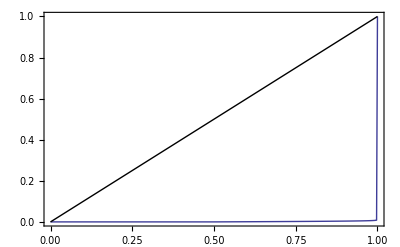

```mathematica
ProbabilityPlot[GompertzMakehamDistribution[0.01,0.3]]
```

```mathematica
InverseFunction[GompertzMakehamDistribution[0.1,0.2] ]
```

InverseFunction[GompertzMakehamDistribution[0.1,0.2]]

```mathematica
foo[x_] := x^3 
InverseFunction[foo][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

x^(1/3)

```mathematica
F[x_] := 1 - Exp[R/G (1 - Exp[G x] )]
InverseFunction[F][x]
```

ConditionalExpression[(2 ⅈ π C[1]+Log[(R+G (2 ⅈ π C[2]+Log[1/(1-x)]))/R])/G,C[2]∈Integers&&C[1]∈Integers]

```mathematica
F[x_] := Exp[ (R t0/n)( 1 - (1 + x/t0)^n )]
InverseFunction[F][x]//Simplify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

t0 (-1+(1-(n Log[x])/(R t0))^(1/n))